#### Code

```mathematica
BlockEncode[A_ ? MatrixQ] := With[{
	Adg = ConjugateTranspose[A]
},
	Join[
		Join[A, MatrixPower[IdentityMatrix[Dimensions[A][[1]]] - A.Adg, 1 / 2], 2],
		Join[MatrixPower[IdentityMatrix[Dimensions[A][[2]]] - Adg.A, 1 / 2], - Adg, 2]
	]
]

PCPhase[phi_, dim_Integer ? Positive, n_Integer ? Positive] :=
	DiagonalMatrix @ Join[
		ConstantArray[Exp[I phi], dim],
		ConstantArray[Exp[- I phi], Max[0, 2 ^ n - dim]]
	]

QSVT[A_ ? MatrixQ, angles_ ? VectorQ, OptionsPattern[{"QSP" -> False}]] := Enclose @ Block[{Π, U, qspQ = TrueQ[OptionValue["QSP"]]},
	Π = With[{n = ConfirmBy[Log2[2 Length[A]], IntegerQ]}, MapIndexed[QuantumOperator[PCPhase[#1, Dimensions[A][[Mod[#2[[1]], 2] + 1]], n], "Label" -> "ϕ"[#]] &, If[qspQ, QSP2QSVTangles[angles], angles]]];
	U = QuantumOperator[BlockEncode[A], "Label" -> "BlockEncode"];
	QuantumCircuitOperator[If[qspQ, Prepend["GlobalPhase"[Pi / 2 (4 - Mod[Length[angles] - 1, 4])]], Identity] @ Riffle[Π, {U, SuperDagger[U]}]]
]

QSP2QSVTangles[angles_] := Block[{newAngles = angles},
	newAngles[[1]] += 3 Pi / 4;
	newAngles[[-1]] -= Pi / 4;
	newAngles[[2 ;; -2]] += Pi / 2;
	newAngles
]

PauliDecompose[qo_QuantumOperator] /; qo["OutputDimensions"] == qo["OutputDimensions"] && MatchQ[qo["OutputDimensions"], {2 ..}] := Block[{
	q = qo["InputQudits"], matrix, coeffs
},
	matrix = 1 / 2 ^ q ArrayReshape[Wolfram`QuantumFramework`PackageScope`kroneckerProduct @@@ Tuples[QuditBasis["Pauli"]["Elements"], q], 4 ^ q {1, 1}];
	coeffs = SparseArray[matrix . qo["StateVector"]];
	{Chop @ coeffs["ExplicitValues"], ArrayReshape[#, Sqrt[Times @@ Dimensions[#]] {1, 1}] & /@ Extract[Inverse @ Transpose @ matrix, coeffs["ExplicitPositions"]]}
]

PauliDecompose[mat_ ? SquareMatrixQ] := PauliDecompose[QuantumOperator[mat]]
```

#### Block encoding

Block encoding allows to embed arbitrary matrix (appropriately normalized) as unitary by introducing a number of auxiliary systems. The simplest way to encode matrix A as unitary U(A) takes the following form: . This form is unitary by construction but requires one to compute matrix square roots:

```mathematica
SeedRandom[0];
A=RandomComplex[{-1-I,1+I},{2,2}];
A/=Norm[A];
```

```mathematica
A//MatrixForm
```

(0.214771+0.613039 ⅈ | 0.187447+0.670773 ⅈ
0.257516-0.368425 ⅈ | 0.0934652+0.193774 ⅈ)

```mathematica
BlockEncode[A]//MatrixForm
```

(0.214771+0.613039 ⅈ | 0.187447+0.670773 ⅈ | 0.101175-2.93472×10^-18 ⅈ | 0.0250842-0.286564 ⅈ
0.257516-0.368425 ⅈ | 0.0934652+0.193774 ⅈ | 0.0250842+0.286564 ⅈ | 0.817873+2.93472×10^-18 ⅈ
0.409125-1.52357×10^-17 ⅈ | -0.439744-0.123481 ⅈ | -0.214771+0.613039 ⅈ | -0.257516-0.368425 ⅈ
-0.439744+0.123481 ⅈ | 0.509923+4.29913×10^-17 ⅈ | -0.187447+0.670773 ⅈ | -0.0934652+0.193774 ⅈ)

The extraction of the corresponding block is done by sandwiching the auxiliary system with 0, which is equivalent to preparing ancilla as empty register and then perform its post-selection using measurement:

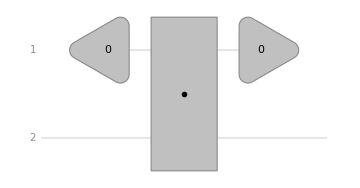

```mathematica
QuantumCircuitOperator[{"0",QuantumOperator[BlockEncode[{{0.1,0.2},{0.3,0.4}}],"Label"->-Graphics-],SuperDagger["0"]}]["Diagram","RotateGateLabel"->False]
```

```mathematica
QuantumCircuitOperator[{"0",QuantumOperator[BlockEncode[A]],QuantumState["0"]ᵀ}]["Matrix"]//MatrixForm
```

(0.214771+0.613039 ⅈ | 0.187447+0.670773 ⅈ
0.257516-0.368425 ⅈ | 0.0934652+0.193774 ⅈ)

In practice it means we can perform multiplication of any normalized vector encoded as a state by an arbitrary matrix:

```mathematica
ψ=QuantumState[b=Normalize@RandomComplex[{-1-I,1+I},2]]
```

QuantumState[…]

```mathematica
A.ψ["StateVector"]
```

{-0.0957408-0.256644 ⅈ,-0.438313+0.185938 ⅈ}

```mathematica
A.ψ["StateVector"]//Abs
```

{0.27392,0.476121}

Only an absolute value of the resulting vector can be estimated from probabilities by usual quantum sampling and then computing a square root:

```mathematica
QuantumCircuitOperator[{"0",ψ->2,QuantumOperator[BlockEncode[A],"Label"->-Graphics-],{1},{2}}][]["Probabilities"]
Sqrt@%
```

<|00→0.0750324,01→0.226691,10→0.310846,11→0.387431|>

<|00→0.27392,01→0.476121,10→0.557535,11→0.622439|>

Another way to encode arbitrary matrix as unitary is first decompose it as a weighted sum of unitaries, for example using Pauli decomposition:

```mathematica
{αk,Uk}=PauliDecompose[A]
```

{{0.154118+0.403407 ⅈ,0.222482+0.151174 ⅈ,0.519599+0.0350346 ⅈ,0.0606528+0.209632 ⅈ},{{{1,0},{0,1}},{{0,1},{1,0}},{{0,ⅈ},{-ⅈ,0}},{{1,0},{0,-1}}}}

```mathematica
αk.Uk-A//Chop
```

{{0,0},{0,0}}

```mathematica
UnitaryMatrixQ/@Uk
```

{True,True,True,True}

Then using the Linear Combination of Unitaries (LCU) technique this decomposition is used to Block Encode the matrix.
LCU consists of first preparing an auxiliary quantum state :

```mathematica
PREP=QuantumState[Sqrt[αk]/Sqrt[Total@Abs[αk]],"Label"->"PREP"]
```

QuantumState[…]

The dimension of which depends on how many non-zero coefficients there are in the decomposition. The state itself is usually implemented by some preparation circuit:

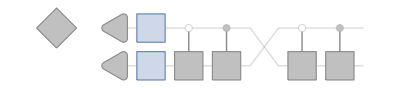

```mathematica
QuantumCircuitOperator[PREP]["Icon"]
```

Selecting corresponding unitaries can be implemented using a Multiplexer:

```mathematica
SEL=QuantumCircuitOperator["Multiplexer"@@Uk,"SEL"];
```

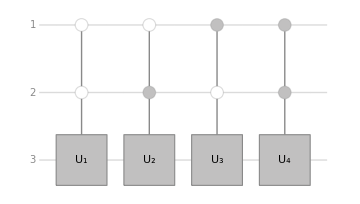

```mathematica
SEL["Diagram"]
```

Then “un-preparing” of auxiliary state is performed as preparation in reverse, with effects at the end in practice implemented as measurements with post-selection:

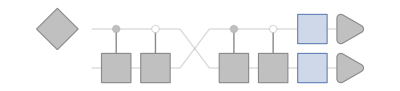

```mathematica
QuantumCircuitOperator[PREP]ᵀ["Icon"]
```

The complete LCU circuit looks very similar to the previous Block Encoding :

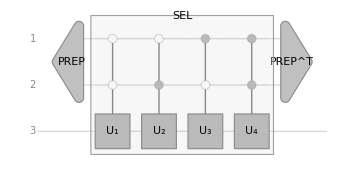

```mathematica
QuantumCircuitOperator[{PREP,SEL,PREPᵀ}]["Diagram"]
```

Which effectively acts as original matrix normalized by :

```mathematica
A/Total@Abs[αk]//Chop//MatrixForm
```

(0.149163+0.42577 ⅈ | 0.130186+0.465868 ⅈ
0.178851-0.25588 ⅈ | 0.0649138+0.134581 ⅈ)

```mathematica
QuantumCircuitOperator[{PREP,SEL,PREPᵀ}]["Matrix"]//Chop//MatrixForm
```

(0.149163+0.42577 ⅈ | 0.130186+0.465868 ⅈ
0.178851-0.25588 ⅈ | 0.0649138+0.134581 ⅈ)

#### QSVT

https://pennylane.ai/qml/demos/tutorial_intro_qsvt

QSVT approximates a polynomial function of a matrix encoded using block encoding by applying a bunch of projector-controlled phase gates with special angles.

Pre-optimized angles approximating 3rd Legendre polynomial:

```mathematica
angles={-0.20409113,-0.91173829,0.91173829,0.20409113};
```

```mathematica
qsvt=QuantumCircuitOperator[QSVT[{{a}},angles],"Parameters"->a];
```

```mathematica
qsvt["Diagram"]
```

-Graphics-

All of which are unitaries:

```mathematica
Through[qsvt[RandomReal[{-1,1}]]["Operators"]["UnitaryQ"]]
```

{True,True,True,True,True,True,True}

```mathematica
qsvtPoly=Chop@FullSimplify[qsvt[]["Matrix"][[1,1]],Assumptions->a∈Reals]
```

a (-1.+2. a^2-0.5 Abs[-1+a^2])

```mathematica
targetPoly=LegendreP[3,a]
```

1/2 (-3 a+5 a^3)

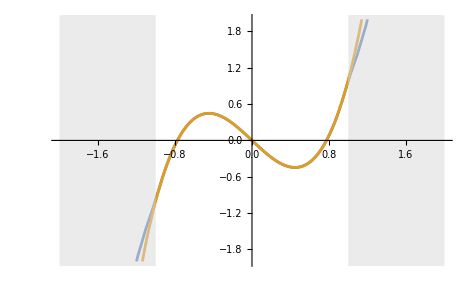

```mathematica
Plot[{qsvtPoly,targetPoly},{a,-2,2},PlotRange->{-2,2},Epilog->{Opacity[0.5],LightGray,Rectangle[{-2,-20},{-1,20}],Rectangle[{1,-20},{2,20}]}]
```

These angles approximate an inverse function 1/x:

```mathematica
kappa=4;
s=0.10145775;
phi={-2.287,2.776,-1.163,0.408,-0.16,-0.387,0.385,-0.726,0.456,0.062,-0.468,0.393,0.028,-0.567,0.76,-0.432,-0.011,0.323,-0.573,0.82,-1.096,1.407,-1.735,2.046,-2.321,2.569,-2.819,-0.011,2.71,-2.382,2.574,0.028,-2.749,2.673,0.062,-2.685,2.416,0.385,-0.387,-0.16,0.408,-1.163,-0.365,2.426};
```

```mathematica
qc=QuantumCircuitOperator[QSVT[{{x}},QSP2QSVTangles@phi],"Parameters"->x]
```

QuantumCircuitOperator[…]

```mathematica
data=Table[Re@QuantumCircuitOperator[QSVT[{{x}},phi,"QSP"->True]]["Matrix"][[1,1]],{x,1/kappa,1,0.1}]
```

{0.396654,0.289517,0.224933,0.183131,0.154461,0.135224,0.119329,0.1072}

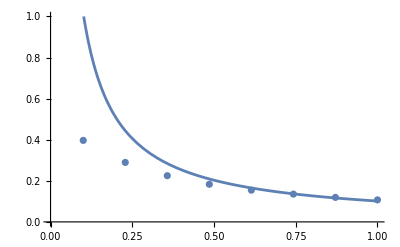

```mathematica
Show[Plot[s/x,{x,0,1},PlotRange->{0,1}],ListPlot[Re@data,DataRange->{0.1,1}]]
```

#### Quantum LinearSolve

Using numerical optimization to find angles to approximate the inverse:

```mathematica
StartExternalSession[
{
"Python", 
"Target" -> <|
"Dependencies" -> {"pennylane","matplotlib"}, 
"EnvironmentName" -> "pennylane",
"PythonRuntime" -> "3.11"
|>
}
];
```

```mathematica
ExternalEvaluate`Private`$Links["DefaultPythonSession"]=SelectFirst[ExternalEvaluate`Private`$Links,#["Target"]["EnvironmentName"]=="pennylane"&];
```

import pennylane as qml
from pennylane import numpy as np

def sum_even_odd_circ(x, phi, ancilla_wire, wires):
    phi1, phi2 = phi[: len(phi) // 2], phi[len(phi) // 2:]

    qml.Hadamard(wires=ancilla_wire)  # equal superposition

    # apply even and odd polynomial approx
    qml.ctrl(qml.qsvt, control=(ancilla_wire,), control_values=(0,))(x, phi1, wires=wires)
    qml.ctrl(qml.qsvt, control=(ancilla_wire,), control_values=(1,))(x, phi2, wires=wires)

    qml.Hadamard(wires=ancilla_wire)  # un-prepare superposition


kappa = 4
s = 0.10145775

np.random.seed(42)  # set seed for reproducibility
phi = np.random.rand(51)

samples_x = np.linspace(1 / kappa, 1, 100)

def target_func(x):
    return s * (1 / x)

def loss_func(phi):
    sum_square_error = 0
    for x in samples_x:
        qsvt_matrix = qml.matrix(sum_even_odd_circ, wire_order=["ancilla", 0])(x, phi, ancilla_wire="ancilla", wires=[0])
        qsvt_val = qsvt_matrix[0, 0]
        sum_square_error += (np.real(qsvt_val) - target_func(x)) ** 2

    return sum_square_error / len(samples_x)

ExternalFunction[…]

# Optimization:
cost = 1
iter = 0
opt = qml.AdagradOptimizer(0.1)

while cost > 0.5e-4:
    iter += 1
    phi, cost = opt.step_and_cost(loss_func, phi)

    if iter % 10 == 0 or iter == 1:
        print(f"iter: {iter}, cost: {cost}")

    if iter > 100:
        print("Iteration limit reached!")
        break

print(f"Completed Optimization! (final cost: {cost})")

phi.tolist()

{0.343276,0.818177,0.630467,0.521469,0.0934962,0.0750699,0.0400572,0.779074,0.371306,0.617287,-0.094845,0.89033,0.969625,0.0731401,0.126368,0.0302208,0.250014,0.338098,0.377905,0.100881,0.564141,0.0231845,0.252858,0.245432,0.424806,0.836973,0.197139,0.568032,0.614735,0.0638299,0.620552,0.16186,0.0713917,0.987031,1.01252,0.556131,0.337498,0.043835,0.706541,0.502659,0.0863033,0.547746,-0.135114,0.973467,0.146631,0.711388,0.322465,0.638504,0.580953,0.182963,1.02138}

```mathematica
phi={0.3432759786772427,0.8181765268442645,0.6304670581702003,0.5214688322696206,0.0934962488150865,0.07506987324898261,0.040057174139855524,0.7790742607336097,0.3713063102548931,0.6172868856116709,-0.0948449872653659,0.890329868617347,0.9696254501050666,0.07314007287599258,0.1263682360122616,0.03022075741159182,0.25001394818890427,0.3380978652367637,0.3779045697179609,0.10088111866951799,0.5641405127746021,0.023184545970391348,0.25285808595198744,0.24543225166284613,0.4248058440469163,0.8369734762385137,0.19713909528080964,0.5680317663248893,0.6147353788255198,0.0638298552796537,0.6205517122822047,0.1618601291139782,0.07139174203090162,0.9870306449003914,1.012518387118901,0.5561313433913494,0.33749773458874094,0.043835000504797904,0.7065414851279866,0.5026587504738946,0.08630330866498175,0.5477461002817865,-0.1351143832314456,0.9734673993926957,0.14663120664557586,0.7113884305091965,0.32246517024439403,0.6385040159652648,0.5809529631913348,0.1829631335937006,1.0213821426100578};
```

This even-odd circuit is used by pennylane to improve approximation, but it is just unnecessary over-complicating the example ... And I couldn’t make it work for smaller matrix ...

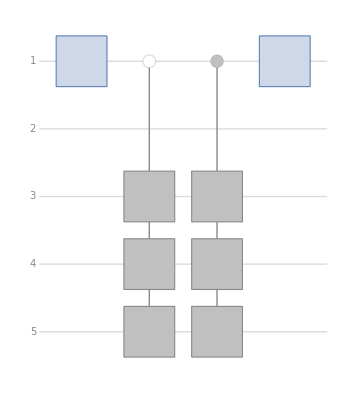

```mathematica
sumEvenOddCirc[A_]:=QuantumCircuitOperator[{"H"->1,
QuantumCircuitOperator[{"C",QSVT[A,phi[[;;Floor[Length[phi]/2]]]]->{3,4,5},{},{1}}],QuantumCircuitOperator[{"C",QSVT[A,phi[[Floor[Length[phi]/2]+1;;]]]->{3,4,5},{1}}],"H"->1}];
sumEvenOddCirc[A]["Diagram","SubcircuitLevel"->0,"ShowGateLabels"->False,"SubcircuitOptions"->"ShowLabel"->False,PlotRangePadding->None]
```

This circuit is using LCU to compute the real part of the matrix: -Graphics-

```mathematica
realCirc=QuantumCircuitOperator[{"H",QuantumCircuitOperator[{"C",QSVT[Transpose@A,phi],{},{1}}],QuantumCircuitOperator[{"C",QSVT[A,phi]["Dagger"],{1}}],"H"}];
```

```mathematica
linearSolve={QuantumState[b]->{3}}/*realCirc;
```

```mathematica
diagram=linearSolve["Flatten"]["Diagram","ShowGateLabels"->False,PlotRangePadding->None];
```

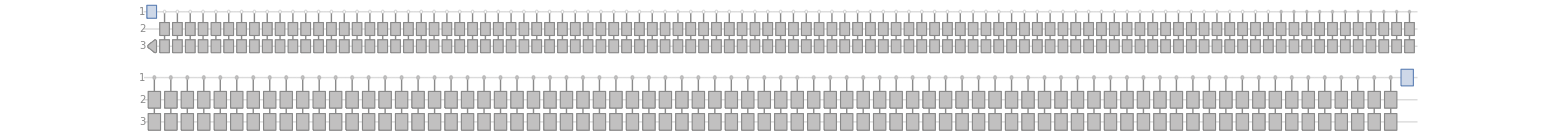

```mathematica
GraphicsColumn[{linearSolve["Flatten"][[;;100]]["Diagram","ShowGateLabels"->False,PlotRangePadding->None],linearSolve["Flatten"][[101;;]]["Diagram","ShowGateLabels"->False,PlotRangePadding->None]}]
```

```mathematica
finalState=linearSolve[];
```

```mathematica
Inverse[A]//MatrixForm
```

(-1.28827 | 2.58366
3.54945 | -2.96027)

```mathematica
realCirc["Matrix"][[;;2,;;2]]/s//Chop//MatrixForm
```

(-1.22033 | 2.5269
3.45226 | -2.85037)

```mathematica
Sqrt@QuantumCircuitOperator[Table[SuperDagger["0"]->q,{q,{1,2}}]][finalState]["Probability"]
```

<|0→0.977479,1→0.211033|>

```mathematica
Normalize@LinearSolve[A,b]
```

{0.980255,0.197738}